### Code (new method of calling new header)

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

### Tests

Select a ruleset to investigate, possibly by giving its reduced rank index, giving it some convenient name:

```mathematica
rs=FromReducedRankIndex[733448814971]
```

<|Index→733448814971,QCode→32342434232423224,RuleSet→{AA→AB,BB→AA,B→AA,A→B}|>

We can pull out the ruleset itself:

```mathematica
rs[["RuleSet"]]
```

{AA→AB,BB→AA,B→AA,A→B}

We generate the sessie and its causal network, again giving it a convenient name:


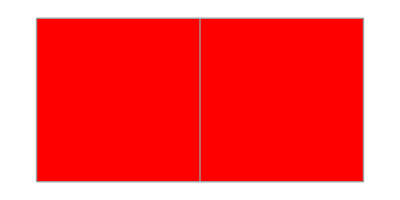

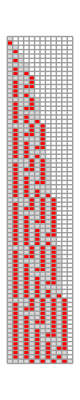
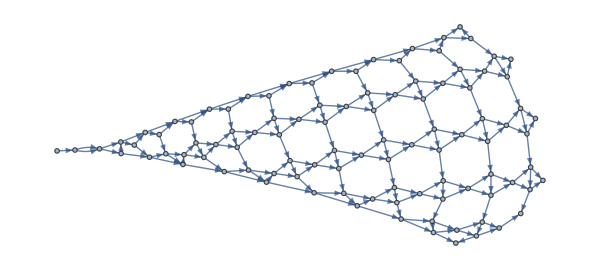
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss=SSS[rs[["RuleSet"]], "A",1000, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->75,NetMax->100,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic]; (* options can be changed or omitted, but these are reasonable choices *)
```

```mathematica
SSSInteractiveDisplay[sss]
```

```mathematica
SetOptions[SSSDisplay,Min->1,Max->400,SSSMin->Automatic,SSSMax->36,NetMin->Automatic,NetMax->Automatic,HighlightMethod->Number,RulePlacement->Bottom,NetMethod->{GraphPlot},ImageSize->161.,NetSize->{Automatic,339.},SSSSize->{Automatic,252.},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False];
```

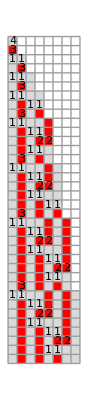
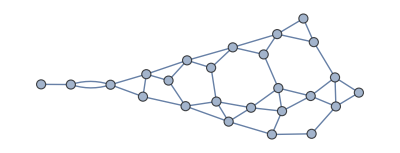
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss,NetMax ->25,VertexLabels->Placed[Automatic,Tooltip]]
```

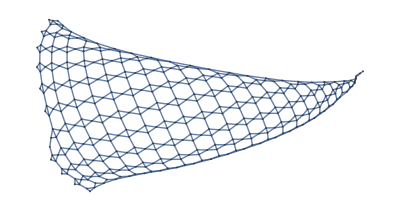
```mathematica
"  "{{-Graphics-}, {{{-Graphics-, "→", -Graphics-}, {-Graphics-, "→", -Graphics-}, {-Graphics-, "→", -Graphics-}, {-Graphics-, "→", -Graphics-}}"Substitution Rules:"}}-Graphics-
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss[["Net"]]//Short
```

{1→2,2→3,2→3,3→4,3→5,4→5,5→6,5→7,6→7,6→8,4→8,«1939»,994→995,994→996,945→996,996→997,945→997,996→998,997→998,997→999,948→999,999→1000,948→1000}

```mathematica
nds=ToNetDifferenceSets[sss[["Net"]]]
```

{{1},{1,1},{1,2},{1,4},{1,2},{1,2},{2,3},{3,4},{1,2},{4,5},{1,2},{1,7},{3,4},{1,2},{5,6},{1,2},{1,2},{4,5},{6,7},{1,2},{7,8},{1,2},{1,2},{6,7},{1,2},{1,10},{6,7},{1,2},{8,9},{1,2},{1,2},{7,8},{1,2},{1,2},{7,8},{9,10},{1,2},{10,11},{1,2},{1,2},{9,10},{1,2},{1,2},{9,10},{1,2},{1,13},{9,10},{1,2},{11,12},{1,2},{1,2},{10,11},{1,2},{1,2},{10,11},{1,2},{1,2},{10,11},{12,13},{1,2},{13,14},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,16},{12,13},{1,2},{14,15},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{15,16},{1,2},{16,17},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,19},{15,16},{1,2},{17,18},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{18,19},{1,2},{19,20},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,22},{18,19},{1,2},{20,21},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{21,22},{1,2},{22,23},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,25},{21,22},{1,2},{23,24},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{24,25},{1,2},{25,26},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,28},{24,25},{1,2},{26,27},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{27,28},{1,2},{28,29},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,31},{27,28},{1,2},{29,30},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{30,31},{1,2},{31,32},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,34},{30,31},{1,2},{32,33},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{33,34},{1,2},{34,35},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,37},{33,34},{1,2},{35,36},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{36,37},{1,2},{37,38},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,40},{36,37},{1,2},{38,39},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{39,40},{1,2},{40,41},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,43},{39,40},{1,2},{41,42},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{42,43},{1,2},{43,44},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,46},{42,43},{1,2},{44,45},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{45,46},{1,2},{46,47},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,49},{45,46},{1,2},{47,48},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{48,49},{1,2},{49,50},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,52},{48,49},{1,2},{50,51},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{51,52},{1,2},{52,53},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1},{},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1}}

You will probably need to limit the part of the nds list that you try to compact, omitting the incomplete sets at the end of the list. In theory it’s not needed to start later than the beginning of the list.

```mathematica
Position[nds,{51,52}]
```

{{904},{909},{912},{915},{918},{921},{924},{927},{930},{933},{936},{939},{942},{945},{948}}

```mathematica
nds[[1;;948]]
```

{{1},{1,1},{1,2},{1,4},{1,2},{1,2},{2,3},{3,4},{1,2},{4,5},{1,2},{1,7},{3,4},{1,2},{5,6},{1,2},{1,2},{4,5},{6,7},{1,2},{7,8},{1,2},{1,2},{6,7},{1,2},{1,10},{6,7},{1,2},{8,9},{1,2},{1,2},{7,8},{1,2},{1,2},{7,8},{9,10},{1,2},{10,11},{1,2},{1,2},{9,10},{1,2},{1,2},{9,10},{1,2},{1,13},{9,10},{1,2},{11,12},{1,2},{1,2},{10,11},{1,2},{1,2},{10,11},{1,2},{1,2},{10,11},{12,13},{1,2},{13,14},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,16},{12,13},{1,2},{14,15},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{15,16},{1,2},{16,17},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,19},{15,16},{1,2},{17,18},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{18,19},{1,2},{19,20},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,22},{18,19},{1,2},{20,21},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{21,22},{1,2},{22,23},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,25},{21,22},{1,2},{23,24},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{24,25},{1,2},{25,26},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,28},{24,25},{1,2},{26,27},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{27,28},{1,2},{28,29},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,31},{27,28},{1,2},{29,30},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{30,31},{1,2},{31,32},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,34},{30,31},{1,2},{32,33},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{33,34},{1,2},{34,35},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,2},{33,34},{1,2},{1,37},{33,34},{1,2},{35,36},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{1,2},{1,2},{34,35},{36,37},{1,2},{37,38},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,2},{36,37},{1,2},{1,40},{36,37},{1,2},{38,39},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{1,2},{1,2},{37,38},{39,40},{1,2},{40,41},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,2},{39,40},{1,2},{1,43},{39,40},{1,2},{41,42},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{1,2},{1,2},{40,41},{42,43},{1,2},{43,44},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,2},{42,43},{1,2},{1,46},{42,43},{1,2},{44,45},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{1,2},{1,2},{43,44},{45,46},{1,2},{46,47},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,2},{45,46},{1,2},{1,49},{45,46},{1,2},{47,48},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{1,2},{1,2},{46,47},{48,49},{1,2},{49,50},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,2},{48,49},{1,2},{1,52},{48,49},{1,2},{50,51},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{1,2},{1,2},{49,50},{51,52},{1,2},{52,53},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52},{1,2},{1,2},{51,52}}

Try the reduction:

```mathematica
rs1=ReduceSetList[nds[[1;;948]]]
```

Transpose::nmtx: The first two levels of {{1,2,8,-1,1,2,6,3,-1,7,«86»},{1,2,17,-1,1,2,15,3,-1,16,«86»},{1,2,26,-1,1,2,24,3,-1,25,«86»},{1,2,35,-1,1,2,33,3,-1,34,«86»},{1,2,44,-1,1,2,42,3,-1,43,«88»}} cannot be transposed.

```mathematica
{{1},{1,1},€_(n$1⊨1)^2[{1,2+2 (-1+n$1)}],€^2[{1,2}],€_(n$1⊨1)^2[{1+n$1,2+n$1}],{1,2},{4,5},€_(n$1⊨1)^2[{1,2+5 (-1+n$1)}],{3,4},{1,2},{5,6},€^2[{1,2}],€_(n$1⊨1)^2[{4+2 (-1+n$1),5+2 (-1+n$1)}],{1,2},{7,8},€^2[{1,2}],{6,7},€_(n$1⊨1)^2[{1,2+8 (-1+n$1)}],€_(n$2⊨1)^2[{6+3 (-1+n$2),7+3 (-1+n$2)},{1,2},{8+2 (-1+n$2),9+2 (-1+n$2)},€^2[€^2[{1,2}],{7+2 (-1+n$2),8+2 (-1+n$2)}]],€_(n$1⊨1)^2[{1,2+11 (-1+n$1)}],€_(n$2⊨1)^2[{9+3 (-1+n$2),10+3 (-1+n$2)},{1,2},{11+2 (-1+n$2),12+2 (-1+n$2)},€^3[€^2[{1,2}],{10+2 (-1+n$2),11+2 (-1+n$2)}]],€_(n$1⊨1)^2[{1,2+14 (-1+n$1)}],€_(n$2⊨1)^2[{12+3 (-1+n$2),13+3 (-1+n$2)},{1,2},{14+2 (-1+n$2),15+2 (-1+n$2)},€^4[€^2[{1,2}],{13+2 (-1+n$2),14+2 (-1+n$2)}]],€_(n$1⊨1)^2[{1,2+17 (-1+n$1)}],€_(n$2⊨1)^2[{15+3 (-1+n$2),16+3 (-1+n$2)},{1,2},{17+2 (-1+n$2),18+2 (-1+n$2)},€^5[€^2[{1,2}],{16+2 (-1+n$2),17+2 (-1+n$2)}]],€_(n$1⊨1)^2[{1,2+20 (-1+n$1)}],€_(n$2⊨1)^2[{18+3 (-1+n$2),19+3 (-1+n$2)},{1,2},{20+2 (-1+n$2),21+2 (-1+n$2)},€^6[€^2[{1,2}],{19+2 (-1+n$2),20+2 (-1+n$2)}]],€_(n$1⊨1)^2[{1,2+23 (-1+n$1)}],€_(n$2⊨1)^2[{21+3 (-1+n$2),22+3 (-1+n$2)},{1,2},{23+2 (-1+n$2),24+2 (-1+n$2)},€^7[€^2[{1,2}],{22+2 (-1+n$2),23+2 (-1+n$2)}]],€_(n$1⊨1)^2[{1,2+26 (-1+n$1)}],€_(n$2⊨1)^2[{24+3 (-1+n$2),25+3 (-1+n$2)},{1,2},{26+2 (-1+n$2),27+2 (-1+n$2)},€^8[€^2[{1,2}],{25+2 (-1+n$2),26+2 (-1+n$2)}]],€_(n$1⊨1)^2[{1,2+29 (-1+n$1)}],€_(n$2⊨1)^2[{27+3 (-1+n$2),28+3 (-1+n$2)},{1,2},{29+2 (-1+n$2),30+2 (-1+n$2)},€^9[€^2[{1,2}],{28+2 (-1+n$2),29+2 (-1+n$2)}]],

€_(n$1⊨1)^2[{1,2+32 (-1+n$1)}],
€_(n$2⊨1)^2[{30+3 (-1+n$2),31+3 (-1+n$2)},{1,2},{32+2 (-1+n$2),33+2 (-1+n$2)},€^10[€^2[{1,2}],{31+2 (-1+n$2),32+2 (-1+n$2)}]],

€_(n$1⊨1)^2[{1,2+35 (-1+n$1)}],
€_(n$2⊨1)^2[{33+3 (-1+n$2),34+3 (-1+n$2)},{1,2},{35+2 (-1+n$2),36+2 (-1+n$2)},€^11[€^2[{1,2}],{34+2 (-1+n$2),35+2 (-1+n$2)}]],

€_(n$1⊨1)^2[{1,2+38 (-1+n$1)}],
€_(n$2⊨1)^2[{36+3 (-1+n$2),37+3 (-1+n$2)},{1,2},{38+2 (-1+n$2),39+2 (-1+n$2)},€^12[€^2[{1,2}],{37+2 (-1+n$2),38+2 (-1+n$2)}]],

€_(n$1⊨1)^2[{1,2+41 (-1+n$1)}],
€_(n$2⊨1)^2[{39+3 (-1+n$2),40+3 (-1+n$2)},{1,2},{41+2 (-1+n$2),42+2 (-1+n$2)},€^13[€^2[{1,2}],{40+2 (-1+n$2),41+2 (-1+n$2)}]],

€_(n$1⊨1)^2[{1,2+44 (-1+n$1)}],
€_(n$2⊨1)^2[{42+3 (-1+n$2),43+3 (-1+n$2)},{1,2},{44+2 (-1+n$2),45+2 (-1+n$2)},€^14[€^2[{1,2}],{43+2 (-1+n$2),44+2 (-1+n$2)}]],
€_(n$1⊨1)^2[{1,2+47 (-1+n$1)}],€_(n$2⊨1)^2[{45+3 (-1+n$2),46+3 (-1+n$2)},{1,2},{47+2 (-1+n$2),48+2 (-1+n$2)},€^15[€^2[{1,2}],{46+2 (-1+n$2),47+2 (-1+n$2)}]],
€_(n$1⊨1)^2[{1,2+50 (-1+n$1)}],
€_(n$2⊨1)^2[{48+3 (-1+n$2),49+3 (-1+n$2)},{1,2},{50+2 (-1+n$2),51+2 (-1+n$2)},€^(16-2 (-1+n$2))[€^2[{1,2}],{49+2 (-1+n$2),50+2 (-1+n$2)}]]}
```

```mathematica
rs1[[-2;;-1]]
```

{€_(n$1⊨1)^2[{1,2+50 (-1+n$1)}],€_(n$2⊨1)^2[{48+3 (-1+n$2),49+3 (-1+n$2)},{1,2},{50+2 (-1+n$2),51+2 (-1+n$2)},€^(16-2 (-1+n$2))[€^2[{1,2}],{49+2 (-1+n$2),50+2 (-1+n$2)}]]}

```mathematica
rs1[[-2;;-1]]//InputForm
```

```mathematica
{IndexedConcatenate[{1, 2 + 50*(-1 + n$1)}, {n$1, 1, 2}], IndexedConcatenate[{48 + 3*(-1 + n$2), 49 + 3*(-1 + n$2)}, {1, 2}, 
  {50 + 2*(-1 + n$2), 51 + 2*(-1 + n$2)}, IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], {49 + 2*(-1 + n$2), 50 + 2*(-1 + n$2)}, 16 - 2*(-1 + n$2)], 
  {n$2, 1, 2}]}/.{48 -> 3n$3, 49 -> 3n$3 + 1, 50 -> 3n$3 + 2, 16 -> n$3, 51 -> 3n$3 + 3}//InputForm
```

{IndexedConcatenate[{1, 2 + (-1 + n$1)*(2 + 3*n$3)}, {n$1, 1, 2}], IndexedConcatenate[{3*(-1 + n$2) + 3*n$3, 1 + 3*(-1 + n$2) + 3*n$3}, {1, 2}, 
  {2 + 2*(-1 + n$2) + 3*n$3, 3 + 2*(-1 + n$2) + 3*n$3}, IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], 
   {1 + 2*(-1 + n$2) + 3*n$3, 2 + 2*(-1 + n$2) + 3*n$3}, -2*(-1 + n$2) + n$3], {n$2, 1, 2}]}

```mathematica
IndexedConcatenate[{IndexedConcatenate[{1, 2 + (-1 + n$1)*(2 + 3*n$3)}, {n$1, 1, 2}], IndexedConcatenate[{3*(-1 + n$2) + 3*n$3, 1 + 3*(-1 + n$2) + 3*n$3}, {1, 2}, 
  {2 + 2*(-1 + n$2) + 3*n$3, 3 + 2*(-1 + n$2) + 3*n$3}, IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], 
   {1 + 2*(-1 + n$2) + 3*n$3, 2 + 2*(-1 + n$2) + 3*n$3}, -2*(-1 + n$2) + n$3], {n$2, 1, 2}]},
  {n$3,1,16}]
```

```mathematica
€_(n$3⊨1)^16[{€_(n$1⊨1)^2[{1,2+(-1+n$1) (2+3 n$3)}],€_(n$2⊨1)^2[{3 (-1+n$2)+3 n$3,1+3 (-1+n$2)+3 n$3},{1,2},{2+2 (-1+n$2)+3 n$3,3+2 (-1+n$2)+3 n$3},€^(-2 (-1+n$2)+n$3)[€^2[{1,2}],{1+2 (-1+n$2)+3 n$3,2+2 (-1+n$2)+3 n$3}]]}]
```

```mathematica
{IndexedConcatenate[{IndexedConcatenate[{1, 2 + (-1 + n$1)*(2 + 3*n$3)}, {n$1, 1, 2}], IndexedConcatenate[{3*(-1 + n$2) + 3*n$3, 1 + 3*(-1 + n$2) + 3*n$3}, {1, 2}, 
  {2 + 2*(-1 + n$2) + 3*n$3, 3 + 2*(-1 + n$2) + 3*n$3}, IndexedConcatenate[IndexedConcatenate[{1, 2}, 2], 
   {1 + 2*(-1 + n$2) + 3*n$3, 2 + 2*(-1 + n$2) + 3*n$3}, -2*(-1 + n$2) + n$3], {n$2, 1, 2}]},
  {n$3,2,5}]}//ExpandAll
```

{{{1,2},{1,10},{6,7},{1,2},{8,9},{1,2},{1,2},{7,8},{1,2},{1,2},{7,8},{9,10},{1,2},{10,11}},{{1,2},{1,13},{9,10},{1,2},{11,12},{1,2},{1,2},{10,11},{1,2},{1,2},{10,11},{1,2},{1,2},{10,11},{12,13},{1,2},{13,14},{1,2},{1,2},{12,13}},{{1,2},{1,16},{12,13},{1,2},{14,15},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{15,16},{1,2},{16,17},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16}},{{1,2},{1,19},{15,16},{1,2},{17,18},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{18,19},{1,2},{19,20},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19}}}

```mathematica
SequencePosition[nds,%165]
```

{}

```mathematica
%15[[10]]
```

```mathematica
€_(n$2⊨1)^2[{21+3 (-1+n$2),22+3 (-1+n$2)},{1,2},{23+2 (-1+n$2),24+2 (-1+n$2)},€^7[€^2[{1,2}],{22+2 (-1+n$2),23+2 (-1+n$2)}]]
```

The most compressed part is

```mathematica
{ExpandAll[%]}
```

Part::take: Cannot take positions 1 through 366 in nds.

{ReduceSetList[nds⟦1;;366⟧]}

```mathematica
GraphPlot[FromNetDifferenceSets@%]
```

```mathematica
Integrate[Integrate[r Exp[-r^2],{r,0,Infinity}],{t,0,Pi/2}]
```

π/4